```mathematica
(*A common efficient algorithm to find the square root of a int is binary search;
In general, there could be better solutions to that;
Here, I compare binary search with the Newton method and show that the latter is asymptotically better;
*)
```

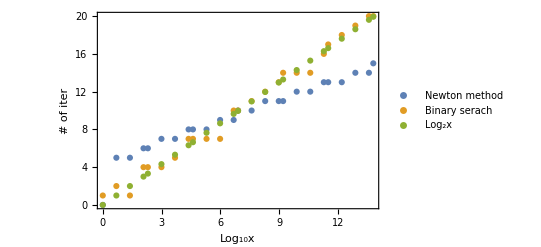

```mathematica
xList={1,2,4,8,10,20,40,80,100,200,400,800,1000,2000,4000,8000,10000,20000,40000,80000,100000,200000,400000,800000,1000000};
xLog=Table[N@Log[x],{x,xList}];
Newton=Partition[Riffle[xLog,Table[
r = x;
count=0;
While[r*r>x,
count+=1;
r=N[(r+x/r)/2]];
count
,{x,xList}]],2];
Log2M=Partition[Riffle[xLog,Table[
Log[2,x]
,{x,xList}]],2];
BinarySearch=Partition[Riffle[xLog,Table[
lower=0;
upper=x+1;
counts =0;
While[lower≤upper,
mid=Floor[(lower+upper)/2];
midS=mid*mid;
counts+=1;
If[midS==x,Break[],If[midS<x,lower=mid+1,upper=mid-1]];
];
counts
,{x,xList}]],2];
ListPlot[{Newton,BinarySearch,Log2M},PlotRange->All,Frame->True,FrameLabel->{{"# of iter",None},{"Log_10x",None}},PlotLegends->{"Newton method","Binary serach","Log_2x"}]
```